```mathematica
P[n_]:=Table[Mod[x+y,n],{x,0,n-1},{y,0,n-1}]
```

```mathematica
M[n_]:=Table[Mod[x y,n],{x,0,n-1},{y,0,n-1}]
```

```mathematica
AI[data_,k_]:=Module[{o={},ld=Length[data]},
For[i=1,i≤ld,i++,
AppendTo[o,Join[{data[[i,1]]},data[[i]]]]];
Return[Prepend[o,Join[{k},Table[s,{s,0,ld-1}]]]]]
```

```mathematica
PlusTable[n_]:=Grid[AI[P[n],"+"], Frame->{{1},{1}}]
```

```mathematica
TimeTable[n_]:=Grid[AI[M[n],"*"],Frame->{{1},{1}}]
```

```mathematica
PlusTable[20]
```

+ | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
0 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 0
2 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 0 | 1
3 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 0 | 1 | 2
4 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 0 | 1 | 2 | 3
5 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 0 | 1 | 2 | 3 | 4
6 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 0 | 1 | 2 | 3 | 4 | 5
7 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 0 | 1 | 2 | 3 | 4 | 5 | 6
8 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
9 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
10 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
11 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
12 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
13 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
14 | 14 | 15 | 16 | 17 | 18 | 19 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
15 | 15 | 16 | 17 | 18 | 19 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
16 | 16 | 17 | 18 | 19 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
17 | 17 | 18 | 19 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
18 | 18 | 19 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
19 | 19 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18

```mathematica
TimesTable[20]
```

* | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
2 | 0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18
3 | 0 | 3 | 6 | 9 | 12 | 15 | 18 | 1 | 4 | 7 | 10 | 13 | 16 | 19 | 2 | 5 | 8 | 11 | 14 | 17
4 | 0 | 4 | 8 | 12 | 16 | 0 | 4 | 8 | 12 | 16 | 0 | 4 | 8 | 12 | 16 | 0 | 4 | 8 | 12 | 16
5 | 0 | 5 | 10 | 15 | 0 | 5 | 10 | 15 | 0 | 5 | 10 | 15 | 0 | 5 | 10 | 15 | 0 | 5 | 10 | 15
6 | 0 | 6 | 12 | 18 | 4 | 10 | 16 | 2 | 8 | 14 | 0 | 6 | 12 | 18 | 4 | 10 | 16 | 2 | 8 | 14
7 | 0 | 7 | 14 | 1 | 8 | 15 | 2 | 9 | 16 | 3 | 10 | 17 | 4 | 11 | 18 | 5 | 12 | 19 | 6 | 13
8 | 0 | 8 | 16 | 4 | 12 | 0 | 8 | 16 | 4 | 12 | 0 | 8 | 16 | 4 | 12 | 0 | 8 | 16 | 4 | 12
9 | 0 | 9 | 18 | 7 | 16 | 5 | 14 | 3 | 12 | 1 | 10 | 19 | 8 | 17 | 6 | 15 | 4 | 13 | 2 | 11
10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10
11 | 0 | 11 | 2 | 13 | 4 | 15 | 6 | 17 | 8 | 19 | 10 | 1 | 12 | 3 | 14 | 5 | 16 | 7 | 18 | 9
12 | 0 | 12 | 4 | 16 | 8 | 0 | 12 | 4 | 16 | 8 | 0 | 12 | 4 | 16 | 8 | 0 | 12 | 4 | 16 | 8
13 | 0 | 13 | 6 | 19 | 12 | 5 | 18 | 11 | 4 | 17 | 10 | 3 | 16 | 9 | 2 | 15 | 8 | 1 | 14 | 7
14 | 0 | 14 | 8 | 2 | 16 | 10 | 4 | 18 | 12 | 6 | 0 | 14 | 8 | 2 | 16 | 10 | 4 | 18 | 12 | 6
15 | 0 | 15 | 10 | 5 | 0 | 15 | 10 | 5 | 0 | 15 | 10 | 5 | 0 | 15 | 10 | 5 | 0 | 15 | 10 | 5
16 | 0 | 16 | 12 | 8 | 4 | 0 | 16 | 12 | 8 | 4 | 0 | 16 | 12 | 8 | 4 | 0 | 16 | 12 | 8 | 4
17 | 0 | 17 | 14 | 11 | 8 | 5 | 2 | 19 | 16 | 13 | 10 | 7 | 4 | 1 | 18 | 15 | 12 | 9 | 6 | 3
18 | 0 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
19 | 0 | 19 | 18 | 17 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1

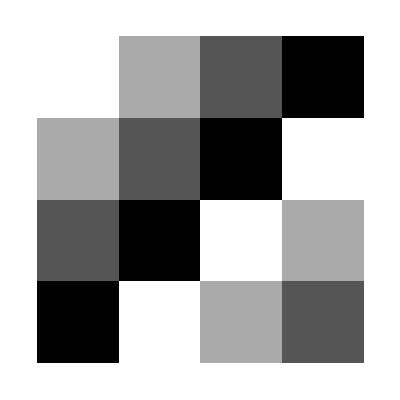
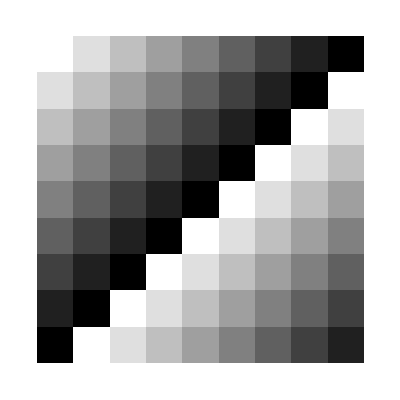
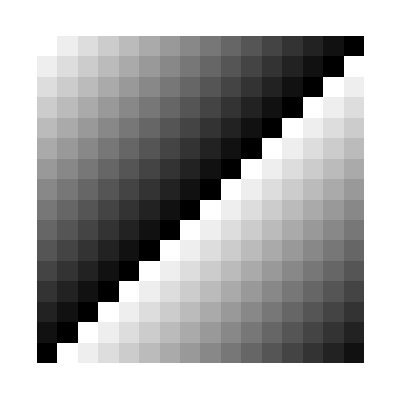
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[P[x^2]],{x,1,10}]
```

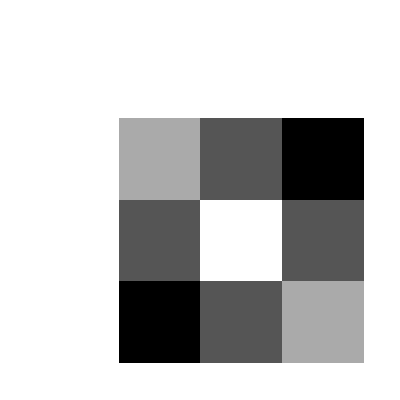
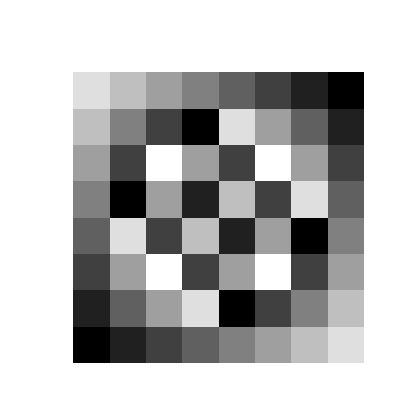
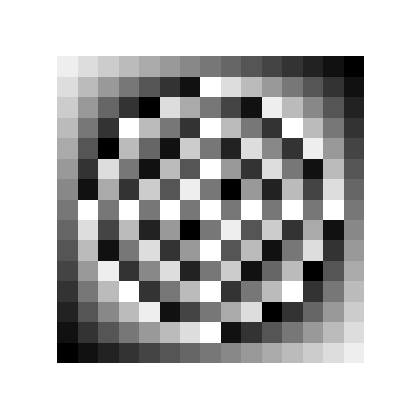
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[M[x^2]],{x,1,10}]
```

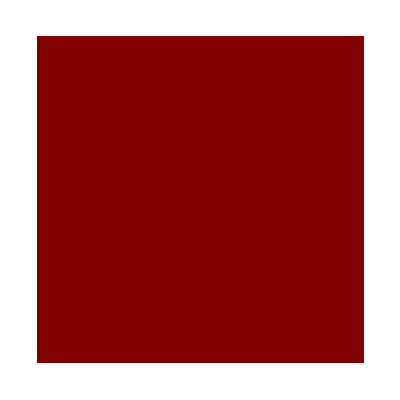
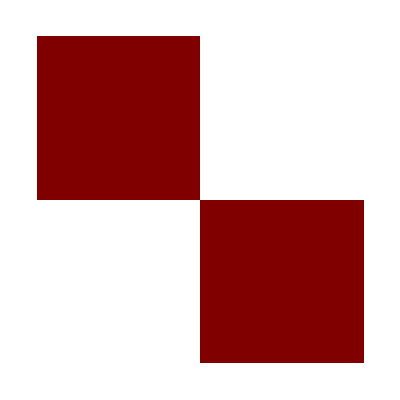
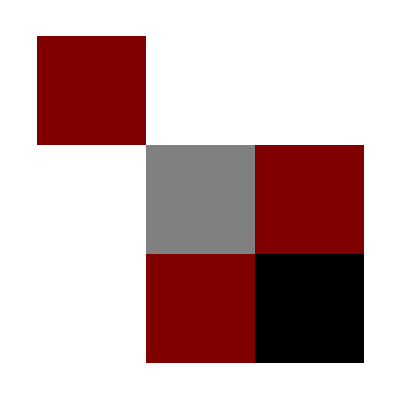
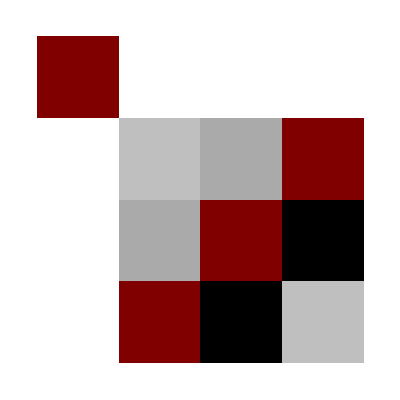
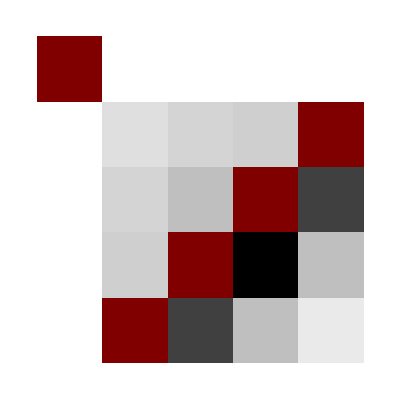
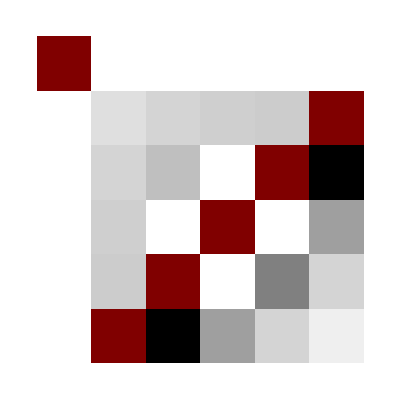
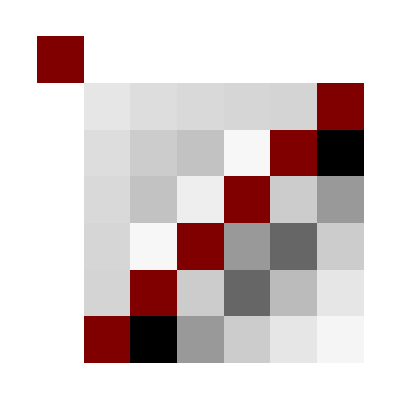
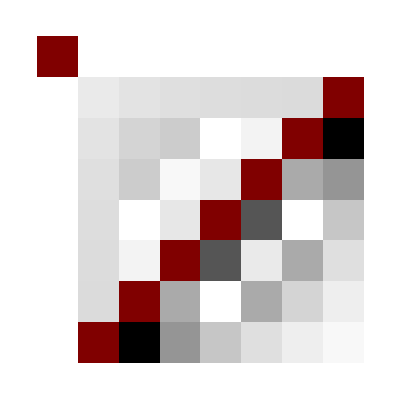

```mathematica
Table[Quiet[ArrayPlot[M[aa]/P[aa]]/.aa->ss],{ss,1,20}]
```